# Data generation

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

## Preparation

```mathematica
Get["/Users/amanokou/SCRIPT-MATHEMATICA/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory["/Users/amanokou/gitsrc/ClusteringAdequation"]
```

/Users/amanokou/gitsrc/ClusteringAdequation

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
anntS[1]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[1]=2;
numClass[1]=3;
numSample[1]={100,100,100};
numBG[1]={0};
```

```mathematica
dimS[1]=StringJoin[Riffle[{ToString[dim[1]],ToString[numClass[1]],ToString[numSample[1]],ToString[numBG[1]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[1]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[1] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[1]=ExportString[centers[1],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844388
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[1]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[1]=Tr[Flatten[distanceMat[centers[1]]]]/(numClass[1]^2-numClass[1])
```

1.73205

```mathematica
samples[1]=Table[Map[#+centers[1][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[1]/2}],RandomReal[{0,2Pi}]}],{numSample[1][[n]]}]],{n,numClass[1]}];
```

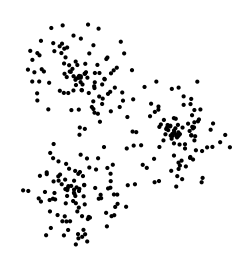

```mathematica
Graphics[Map[Point[#]&,samples[1],{2}]]
```

```mathematica
samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";
```

```mathematica
(*Export["data1.tsv",strDataToExportStr[1],"String"]*)
```

### data 2 (unbalanced)

```mathematica
anntS[2]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[2]=2;
numClass[2]=3;
numSample[2]={200,100,50};
numBG[2]={0};
```

```mathematica
dimS[2]=StringJoin[Riffle[{ToString[dim[2]],ToString[numClass[2]],ToString[numSample[2]],ToString[numBG[2]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[2]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[2]=ExportString[centers[2],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[2]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[2]=Tr[Flatten[distanceMat[centers[2]]]]/(numClass[2]^2-numClass[2])
```

1.01673

```mathematica
radius[2]={distMean[2]*0.6,distMean[2]*0.4,distMean[2]*0.2}
```

{0.61004,0.406693,0.203347}

```mathematica
samples[2]=Table[Map[#+centers[2][[n]]&,Table[polarToxy[{RandomReal[{0,radius[2][[n]]}],RandomReal[{0,2Pi}]}],{numSample[2][[n]]}]],{n,numClass[2]}];
```

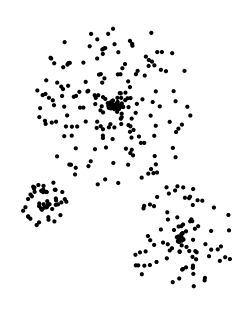

```mathematica
Graphics[Map[Point[#]&,samples[2],{2}]]
```

```mathematica
samplesS[2]=ExportString[Flatten[samples[2],1],"TSV"]<>"\n";
```

```mathematica
(*Export["data2.tsv",strDataToExportStr[2],"String"]*)
```

### data 3 (noisy)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844388
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.52987,-1.01582},{1.43231,-1.4003}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

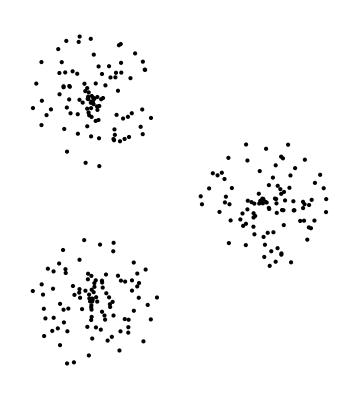

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

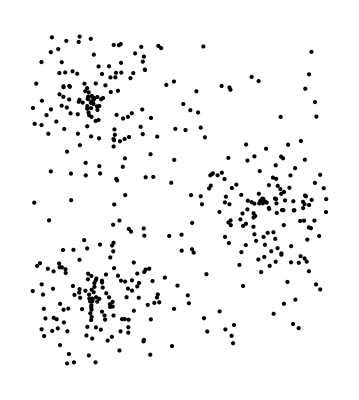

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*Export["data3.tsv",strDataToExportStr[3],"String"]*)
```

data3.tsv

### data 4 (sub class)

```mathematica
anntS[4]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[4]=2;
numClass[4]=4;
numSample[4]={100,100,100,100};
numBG[4]={0};
```

```mathematica
dimS[4]=StringJoin[Riffle[{ToString[dim[4]],ToString[numClass[4]],ToString[numSample[4]],ToString[numBG[4]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[4]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[4]=ExportString[centers[4],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])
```

3.49071

```mathematica
samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];
```

```mathematica
maxmin[4]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[4,"class"],1]]]
```

{{2.84335,-2.83036},{1.80755,-1.85934}}

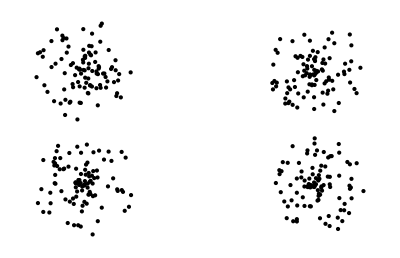

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[4,"class"],1]]]
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[4]=ExportString[Flatten[samples[4,"class"],1],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

```mathematica
(*Export["data4.tsv",strDataToExportStr[4],"String"]*)
```

### data 5 (ring + disc)

```mathematica
anntS[5]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[5]=2;
numClass[5]=2;
numSample[5]={100,200};
numBG[5]={0};
```

```mathematica
dimS[5]=StringJoin[Riffle[{ToString[dim[5]],ToString[numClass[5]],ToString[numSample[5]],ToString[numBG[5]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[5]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[5]=ExportString[centers[5],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
(*distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])*)
```

```mathematica
(*samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];*)
```

```mathematica
samples[5,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[5][[1]]}]];
```

```mathematica
samples[5,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[5][[2]]}]];
```

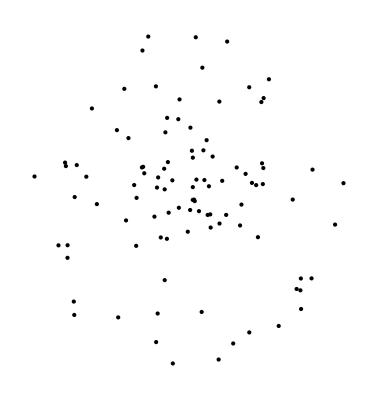

```mathematica
Graphics[Map[Point[#]&,samples[5,"disc"]]]
```

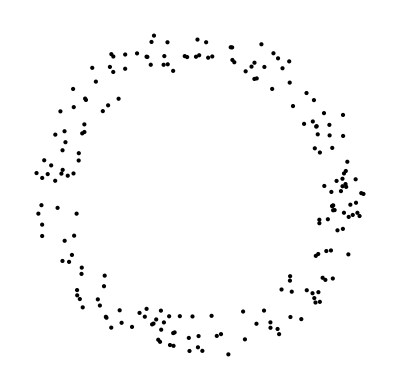

```mathematica
Graphics[Map[Point[#]&,samples[5,"ring"]]]
```

```mathematica
samples[5,"class"]=Join[samples[5,"disc"],samples[5,"ring"]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[5]=ExportString[Flatten[samples[5,"class"],1],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

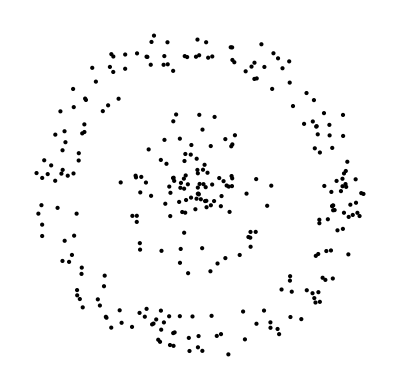

```mathematica
Map[Point[#]&,samples[5,"class"]]//Graphics
```

```mathematica
(*Export["data5.tsv",strDataToExportStr[5],"String"]*)
```

data5.tsv

### data 6 (spiral)

```mathematica
anntS[6]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[6]=2;
numClass[6]=3;
numSample[6]={100,100,100};
numBG[6]={0};
```

```mathematica
dimS[6]=StringJoin[Riffle[{ToString[dim[6]],ToString[numClass[6]],ToString[numSample[6]],ToString[numBG[6]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[6]={{,},{,},{,}}
```

{{Null,Null},{Null,Null},{Null,Null}}

```mathematica
origins[6]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
centersS[6]=ExportString[centers[6],"TSV"]<>"\n"
```

```mathematica
(samples[6,0]=Table[{r,3r},{r,0.5,3-0.02,0.025}])//Length
```

100

```mathematica
(samples[6,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
(samples[6,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
(samples[6,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
samples[6,"class"]=Join[samples[6,0],samples[6,1],samples[6,2]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[6]=ExportString[Flatten[samples[6,"class"],1],"TSV"]<>"\n";
```

```mathematica
(*samplesS[4]=ExportString[Join[Flatten[samples[4,"class"],1],samples[4,"background"]],"TSV"]<>"\n";*)
```

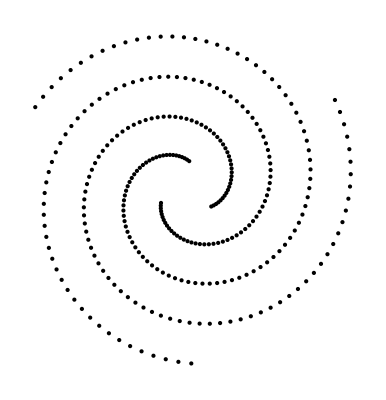

```mathematica
Map[Point[#]&,samples[6,"class"]]//Graphics
```

```mathematica
(*Export["data6.tsv",strDataToExportStr[6],"String"]*)
```

data6.tsv

## 3D

### data 7 (chain)

```mathematica
anntS[7]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[7]=3;
numClass[7]=2;
numSample[7]={150,150};
numBG[7]={0};
```

```mathematica
dimS[7]=StringJoin[Riffle[{ToString[dim[7]],ToString[numClass[7]],ToString[numSample[7]],ToString[numBG[7]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[7]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

{{0,0},{0,0},{0,0}}

```mathematica
centersS[7]=ExportString[centers[7],"TSV"]<>"\n"
```

0	0	0
1	0	0

//Under construcrion

```mathematica
samples[7,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi,2Pi/149}]];
```

```mathematica
Map[Point[#]&,samples[7,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[7,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi,2Pi/149}]];
```

```mathematica
Map[Point[#]&,samples[7,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(samples[7,"All"]=Join[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length
```

300

```mathematica
Map[Point[#]&,samples[7,"All"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[7]=ExportString[Flatten[samples[7,"All"],1],"TSV"]<>"\n";
```

```mathematica
Export["data7.tsv",strDataToExportStr[7],"String"]
```

data7.tsv

## high Dimensional

## Experimental

```mathematica
Map[polarToxy[{1,#}]&,Table[2Pi/3 n,{n,0,2}]]
```

{{1,0},{-1/2,(√3)/2},{-1/2,-(√3)/2}}

```mathematica
Graphics[Map[Point[#]&,Map[polarToxy[{1,#}]&,Table[2Pi/3 n,{n,0,2}]]]]
```

-Graphics-